```mathematica
dd[n_,g_,T_] := Chop[1/(2 Pi)NIntegrate[Exp[- I n ϕ] √((1 - g Exp[I ϕ])/(1- g Exp[-I ϕ]))Tanh[1/T((1 - g Exp[I ϕ])(1- g Exp[-I ϕ]))^(1/2)]/.ϕ -> ϕ - 0.000001 I,{ϕ,0,2 Pi},AccuracyGoal->6,WorkingPrecision->8,MaxRecursion->20]] 
toep[n_,g_,T_] := Table[dd[i-j,g,T],{i,n},{j,n}]
toep2[n_,g_,T_] := Table[dd2[i-j,g,T],{i,n},{j,n}]
```

```mathematica
dd[12,1.5,1] //Timing
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.14518,0.035924597}

```mathematica
toepmod[n_,g_,T_] := Table[dd[i-j],{i,n},{j,n}]
teopswap = toepmod[5,1,1]
```

{{dd[0],dd[-1],dd[-2],dd[-3],dd[-4]},{dd[1],dd[0],dd[-1],dd[-2],dd[-3]},{dd[2],dd[1],dd[0],dd[-1],dd[-2]},{dd[3],dd[2],dd[1],dd[0],dd[-1]},{dd[4],dd[3],dd[2],dd[1],dd[0]}}

```mathematica
teopswap[[All,5]] = Table[dd[i],{i,5}]
```

{dd[1],dd[2],dd[3],dd[4],dd[5]}

```mathematica
teopswap // MatrixForm
```

(dd[0] | dd[-1] | dd[-2] | dd[-3] | dd[1]
dd[1] | dd[0] | dd[-1] | dd[-2] | dd[2]
dd[2] | dd[1] | dd[0] | dd[-1] | dd[3]
dd[3] | dd[2] | dd[1] | dd[0] | dd[4]
dd[4] | dd[3] | dd[2] | dd[1] | dd[5])

```mathematica
(*     <<Subscript[A, 0](t)Subscript[A, n](0)(>>)_β     *)
eps[p_,g_] := 2 √(1 + g^2 - 2 g Cos[p]); 
ffd[ϵ_, T_] := 1/(1 + Exp[ϵ/T]);
ACorr0t[n_,g_,T_,t_] := Chop[1/(2 Pi)NIntegrate[Chop[Exp[I n p] (Exp[I eps[p,g]t] ffd[eps[p,g],T] + Exp[-I eps[p,g]t] ffd[-eps[p,g],T])] /. p -> p + I 0.0000001, {p,0,2 Pi}, AccuracyGoal->6]];
ACorr0t2[n_,g_,T_,t_] := Chop[1/M Sum[Chop[Exp[I n p] (Exp[I eps[p,g]t] ffd[eps[p,g],T] + Exp[-I eps[p,g]t] ffd[-eps[p,g],T])], {p,0,2 Pi, 2 Pi/M}]];
```

```mathematica
ACorr0t[50,1,1, 10]  //Timing
Chop[N[ACorr0t2[50,1,1,10] ]]//Timing
```

{0.041931,0}

$Aborted

The formula  : ⟨σ_0^z(t) σ_n^z(0)⟩_β = ∑_(i = 0)^n [⟨A_0(t)A_i(0)⟩   (-1)^(1 + δ_(i,0))  toep_(rank = n)[A_i->A_0]]

```mathematica
tim = AbsoluteTime[];
n = 10; 
g = 1;
T = 1;
t = 10;
dd2list = <|Table[i -> Chop[N[dd2[i,g,T]]] , {i,-n,n}]|> ;
tim1 = AbsoluteTime[];
Print["The time taken to construct the dd2list is ", tim1 - tim]
ttmat =  Table[dd2list[i-j],{i,n},{j,n}];
tim2 = AbsoluteTime[];
Print["Time taken to construct ttmat is ", tim2 - tim1]
insrow = Table[dd2list[i],{i,n}];
tim3 = AbsoluteTime[];
Print["Time taken to construct insrow is ", tim3 - tim2]
init = Chop[N[ACorr0t2[0,g,T,t] * Det[ttmat]]]; 
tim4 = AbsoluteTime[];
Print["Time taken to initialize init is ", tim4 - tim3]
For[i=1,i≤n,i++, 
tim5 = AbsoluteTime[];
swapmat = ttmat ;
tim6 = AbsoluteTime[];
PrintTemporary["i = ", i, " The time taken to initialize swapmat is ",tim6 - tim5];
swapmat[[All,i]] = insrow;
tim7 = AbsoluteTime[];
init = init - Chop[N[(ACorr0t2[i,g,T,t]* Det[swapmat]) ]]; 
PrintTemporary["i = ",i," The time taken to compute the determinant is ", tim7 - tim6]
]
Print["The total time taken at the end is ", AbsoluteTime[]-tim]
N[init]//Simplify
```

The time taken to construct the dd2list is 2.76274

Time taken to construct ttmat is 0.00131

Time taken to construct insrow is 0.000799

Time taken to initialize init is 0.14574

The total time taken at the end is 4.761408

0.00103971-0.00164211 ⅈ

```mathematica
ttmat // MatrixForm
```

$Aborted

```mathematica
M = 1000;
dd2[n_,g_ ,T_] :=Chop[ 1/M Sum[Chop[Exp[- I n ϕ] √((1 - g Exp[I ϕ])/(1- g Exp[-I ϕ]))Tanh[1/T((1 - g Exp[I ϕ])(1- g Exp[-I ϕ]))^(1/2)]], {ϕ,0 + 2 Pi/M,2Pi(1-1/M), 2 Pi/M}]]
```

```mathematica
dd2[100,1.5,1] //Timing
```

{0.040116,0.002662}

```mathematica
NSolve[((1 - 1.5Exp[I ϕ])(1- 1.5 Exp[-I ϕ]))^(1/2)== 3I Pi/2 ,ϕ]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→0.-2.82802 ⅈ},{ϕ→0.+2.82802 ⅈ}}

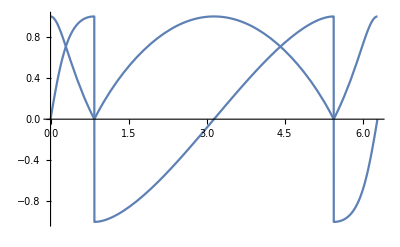

```mathematica
Plot[ReIm[√((1 - 1.5Exp[I ϕ])/(1-  1.5Exp[-I ϕ]))]/. ϕ -> ϕ - 0.000001I ,{ϕ ,0,2Pi}]
```

```mathematica
n=15;
Chop[N[dd2[n,1.1,1]]]
dd[n,1.1,1]
```

-0.0190676

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-0.019001401

## See how recalling the answer from a key-value pair list is 10000 times faster than actually computing the function !!!!

```mathematica
dd2list = <|Table[i -> dd2[i,g,T] , {i,-100,100}]|> ;
dd2list[-29] // Timing 
dd2[-29,g,T] // Timing
```

{8.×10^-6,0.0115543}

{0.034421,0.0115543}

```mathematica
For[i = 1, i< 5, i++, 
temp = PrintTemporary["i = ", i];
Pause[2 ]; 
NotebookDelete[temp]];
```

```mathematica
mat = Table[RandomReal[], {i,100}, {j,100}] ;
Det[mat] //Timing (* Bottom-line : it takes 0.5 millisecond to compute the determinant of a 100x100 matrix *)
```

{0.000572,-6.19005×10^26}

## Find how much time it takes to compute a 100x100 determinant

```mathematica
M = 1000;
dd2[n_,g_ ,T_] :=Chop[ 1/M Sum[Chop[Exp[- I n ϕ] √((1 - g Exp[I ϕ])/(1- g Exp[-I ϕ]))Tanh[1/T((1 - g Exp[I ϕ])(1- g Exp[-I ϕ]))^(1/2)]], {ϕ,0 + 2 Pi/M,2Pi(1-1/M), 2 Pi/M}]]
n = 100; 
g = 1;
T = 1;
t = 10;
dd2list = <|Table[i -> Chop[N[dd2[i,g,T]]] , {i,-n,n}]|> ;
ttmat =  Table[dd2list[i-j],{i,n},{j,n}];
Det[ttmat] // Timing
```

{0.037704,6.88532×10^-19}

```mathematica
dd2list[5] // Timing
Chop[N[dd2[5,1,1]]] //Timing
```

{0.000021,-0.00119325}

{0.155849,-0.00119325}

## The exact CFT result at critical coupling : g=1

```mathematica
epsilon = 10^-3;
exact[x_,t_, T_] := -I (2 Pi^2 T^2)^(1/4)* (1/((Sinh[Pi T *(x-t + I epsilon)])* Sinh[Pi T * (x+t - I epsilon)]))^(1/4)
```

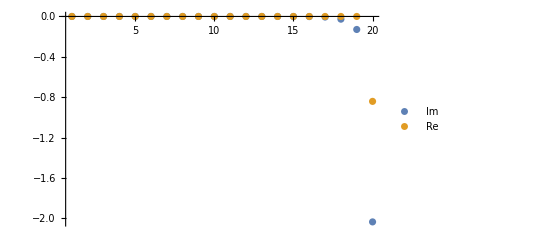

```mathematica
xlist = Range[20];
tlist = Range[20]; 
T = 1; 
exactlist = Table[Chop[N[exact[x,t,T]]], {x,-20,-1}, {t,20}];
ListPlot[{Im[exactlist[[All,1]]],Re[exactlist[[All,1]]]}, PlotLegends->{"Im", "Re"}, PlotRange->Full]
(*exactlist[[15,1]]*)
```

## Performing the Discrete Fourier transform

```mathematica
Fourier[{{1,2},{3,4}}]
```

{{5.,-1.},{-2.,0.}}

## Fixing branch points in NIntegrate

```mathematica
branfunc[ϕ_] := √((1 - 1.5  Exp[I ϕ])/(1-  1.5  Exp[-I ϕ]));  (* Here ϕ is a real number, and the function has a branch cut : z = g Exp[I ϕ] is a complex number *)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {0.84666}. NIntegrate obtained 4.-1.54911×10^-15 ⅈ and 0.00352148 for the integral and error estimates.

4.

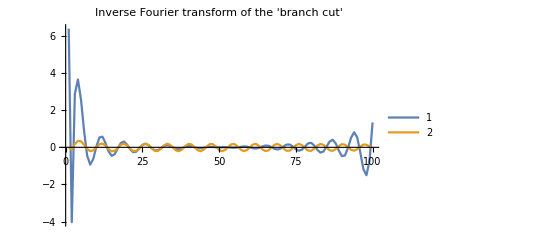

```mathematica
Chop[NIntegrate[Chop[branfunc[(ϕ+ 0.00000001I)]],{ϕ,0,2 Pi}]]
invfouBran = InverseFourier[Array[branfunc,100,{0,2Pi}]];
ListLinePlot[{Re[invfouBran],Im[invfouBran]}, PlotLegends->Automatic, PlotRange->Full, PlotLabel->"Inverse Fourier transform of the 'branch cut' - done numerically"]
```

```mathematica
(* This function looks like it's the Fourier transform of something normal(ish?) *)
```

```mathematica
compbranfunc[z_] :=  √((1 - z)/(1- Conjugate[z]));
NSolve[Reduce[1-  1.5Exp[-I ϕ] == 0]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→0.-0.405465 ⅈ}}

```mathematica
(*ddf[n_,g_,T_] := FourierCoefficient[√((1 - g Exp[I ϕ])/(1- g Exp[-I ϕ]))Tanh[1/T((1 - g Exp[I ϕ])(1- g Exp[-I ϕ]))^(1/2)]/.ϕ -> ϕ-Pi,ϕ,n] )*
ddf[12,1.5,1]
```

$Aborted

```mathematica
N[FourierCoefficient[√((1 - 1.5 Exp[I ϕ])/(1- 1.5 Exp[-I ϕ]))Tanh[1/1((1 - 1.5 Exp[I ϕ])(1- 1.5 Exp[-I ϕ]))^(1/2)], ϕ,5, Assumptions->Element[ϕ,Reals]]]
```

$Aborted

## Comparing the equal time result from Sachdev with numerics

```mathematica
sachchikw[ω_,k_,T_] := 1/T^(7/4)  (Gamma[1/16 - I (ω + k)/(4Pi T)] Gamma[1/16 - I (ω - k)/(4Pi T)])/(Gamma[15/16 - I (ω + k)/(4Pi T)] Gamma[15/16 - I (ω - k)/(4Pi T)])
discSach = Flatten[Array[sachchikw,{100,100,1},{{0,2Pi},{0,2Pi},1}],1]; (* This is just the imaginary part - do Kramer-Kronig first! But what's the formula for a function of two variables? *)
discSachTX=InverseFourier[discSach];
ListPlot[discSachTX[[1,All]]]
```

-Graphics-

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.558971,0.365199,0.240634,0.158661,0.104619,0.0689841,0.0454872,0.0299937,0.0197774,0.013041,0.00859904,0.00567009,0.00373878,0.0024653,0.00162559,0.00107189,0.000706791,0.000466049,0.000307306,0.000202634,0.000133614,0.0000881033,0.0000580941,0.0000383065,0.0000252588}

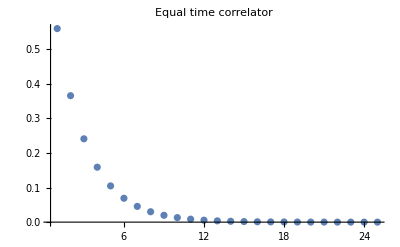

{{0.55897094}}

```mathematica
(*greenspacetime = InverseFourier[Table[sachchikw[ω,k,1],{ω,0,2Pi},{k,0,2Pi}]]; (*This is useless and you're wasting your time if you do Kramer-Kronig*)
ListPlot[greenspacetime[[1,All]]]*)
nmax = 25; (* Maximum number of sites for which the correlator is obtained *)
g = 1;
T = 1; 
corrln = Table[0 , {i,nmax}];
(*dd2list = <|Table[i -> Chop[N[dd2[i,g,T]]] , {i,-nmax,nmax}]|> ;*)
ddlist = <|Table[i -> Chop[N[dd[i,g,T]]] , {i,-nmax,nmax}]|> ;
For[ n = 1 , n  ≤ nmax, n++ ,  
ttmat = Table[ddlist[i-j],{i,n},{j,n}] ; ; 
 corrln[[n]] = N[Chop[Det[ttmat]]];
] 
corrln
ListPlot[Abs[corrln],PlotRange->Full, PlotLabel->"Equal time correlator"]
```

## Checking the built-in FFT

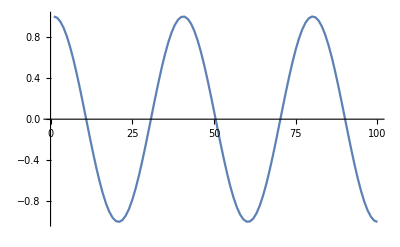

```mathematica
y= Array[Cos,100,{0,5Pi}];
ListLinePlot[y]
```

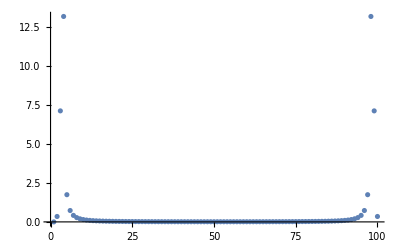

```mathematica
Y = Fourier[y];
ListPlot[Abs[Y]^2, PlotRange->Full]
```

```mathematica
(*period = 40, frequency = (2Pi)/40: 0->Pi are the positive frequencies and Pi-> 2Pi are the negative frequencies. The 4th point => 2Pi/100 * 3 = 2Pi/33. Note how zero freq is the 1st point *)
```

```mathematica
(*  10 * 2Pi/100 = 2Pi/10;  *)
ListLinePlot[Chop[InverseFourier[Y]]]
```

-Graphics-

```mathematica
Flatten[Array[f,{5,5,1},{{0,1},{0,1},1}],1]
```

{25,1}